# Question 1

## PART i)

#### State equation matrices :

```mathematica
A=({{10, 1}, {1, -2}});B=({{0}, {1}});Cm=({{1, 1}});
```

#### Controllability :

```mathematica
n=Dimensions[A][[1]];
r=Dimensions[B][[2]];
m =Dimensions[Cm][[1]];
Print["n = ", n,"\t r = ",r,"\t m = ",m]
P=Join[B,A.B, 2];
Print["P = ",MatrixForm[P]]
Print["Rank of P: ",MatrixRank[P]]
If[MatrixRank[P]==n,Print["System is controllable."],Print["System is uncontrollable."]]
```

n = 2	 r = 1	 m = 1

P = (0 | 1
1 | -2)

Rank of P: 2

System is controllable.

#### Observability :

```mathematica
Q=Join[Cmᵀ,Aᵀ.Cmᵀ,2];
Print["Q = ",MatrixForm[Q]]
Print["rank(Q) = ",MatrixRank[Q]]
If[MatrixRank[Q]==n,Print["System is observable."],Print["System is not observable."]]
```

Q = (1 | 11
1 | -1)

rank(Q) = 2

System is observable.

```mathematica
Eigenvalues[A]//N
```

{10.0828,-2.08276}

One of the eigenvalue is positive. Thus, the system is unstable.

## PART ii)

#### I will use the following approach: x(0)=Q^-1 y(0)-Q^-1 T u(0)

Print["Cm.b equals to",Cm.B ]
TT= (0 | 0
1 | 0); (*T matrix in the course notes. *)
TT //MatrixForm

Cm.b equals to{{1}}

(0 | 0
1 | 0)

#### y(0)=(y[0] y'[0]), u0=(u[0] u'[0])

```mathematica
Y0=({{3}, {1}});
U0=({{1}, {0}});
```

```mathematica
X0=Inverse[Q].Y0-Inverse[Q].TT.U0;
Print["x[0]=", X0 //MatrixForm]
```

x[0]=(1/4
1/4)

## PART iii) Transfer Function

```mathematica
Inn=IdentityMatrix[n];
```

```mathematica
G[s]=(Cm.Inverse[s Inn-A].B//Flatten //Simplify)[[1]]//Simplify;
Print["G(s) = ",G[s]]
```

G(s) = (-9+s)/(-21-8 s+s^2)

```mathematica
Solve[Denominator[G[s]]==0,s]//Flatten
```

{s→4-√37,s→4+√37}

System is unstable!

## Part iv) Controllable and Observable Canonical Form

## I did this part by hand . Please check the papers given to you (Page 1).

# Question 2

```mathematica
Quit[]
```

```mathematica
G[s]=({{1/(s+2), (s-1)/(s+1)}, {(3s)/(s+2), 2/(s+1)}});Print["G(s) = ",G[s],"\nlim_(s → ∞)  G(s) = ",Limit[G[s],s->∞]]
```

G(s) = {{1/(2+s),(-1+s)/(1+s)},{(3 s)/(2+s),2/(1+s)}}
lim_(s → ∞)  G(s) = {{0,1},{3,0}}

G(s) is not strictly proper. We need to convert that before continue.

```mathematica
DD=({{0, 1}, {3, 0}});
H[s]=DD-G[s]//Simplify;
Print["H(s) = ",H[s]//MatrixForm,"\nlim_(s → ∞)  H(s) = ",Limit[H[s],s->∞]//MatrixForm]
```

H(s) = (-1/(2+s) | 2/(1+s)
6/(2+s) | -2/(1+s))
lim_(s → ∞)  H(s) = (0 | 0
0 | 0)

Now H (s) is strictly proper!

#### ExtendedHermiteForm and other helpful functions given in course documents:

ExtendedHermiteForm[A,s] yields the Hermite form H of a matrix A of polynomials in s. The result is a list {H,U} such that H=U.A with U unimodular

```mathematica
myBlockDiagonalMatrix[b:{__?MatrixQ}]:=Module[{r,c,n=Length[b],i,j},{r,c}=Transpose[Dimensions/@b];
ArrayFlatten[Table[If[i==j,b[[i]],ConstantArray[0,{r[[i]],c[[j]]}]],{i,n},{j,n}]]];
FindMin[at_,kt_,xt_,pt_]:=Module[{a=at,k=kt,x=xt,p=pt,i,rgmin,degmin},For[i=k;rgmin=k;degmin=+Infinity,i≤p,i++,If[a[[i]]=!=0&&Exponent[a[[i]],x]<degmin,rgmin=i;
degmin=Exponent[a[[i]],x]]];
rgmin];

Variabile[at_]:=Module[{a=at,xt},xt=Variables[a];
If[xt==={},d,xt[[1]]]];

ExtPolQ[lt_List,xt_:{}]:=Module[{x=xt},
If[x==={}&&Length[Variables[lt]]>1,Message[General::badarg];
Return[$Failed],If[x==={},x=Variabile[lt]]];
(*If all the components of lt are polynomials in x*)Apply[And,PolynomialQ[#,x]&/@Flatten[lt]]||(*or in x^-1,the function returns True,False otherwise.(Substituting all the symbols x^-n->x^n we can use PolynomialQ also in this case)*)Apply[And,PolynomialQ[#,x]&/@Flatten[Expand[lt]/.{(x^(n:_))->(x^-n),x->x^-1}]]];

ExtendedHermiteForm[at_,xt_:{}]:=Module[{a=at,p,m,x=xt,u,v,k,kcl,i,j,q,deg,esp,coef,rg,rmin,upc,lpc,ch=False},If[x==={}&&Length[Variables[a]]>1,Message[General::badarg];
Return[$Failed],If[x==={},x=Variabile[a]]];
If[Not[ExtPolQ[a,x]],Message[General::pol];Return[$Failed]];
If[Not[Apply[And,PolynomialQ[#,x]&/@Flatten[a]]],a=a/.{(x^(n:_))->(x^-n)};
ch=True];
(*Initialize the variables*){p,m}=Dimensions[a];
u=IdentityMatrix[p];
(*Main loop on k (and kcl)*)For[k=1;kcl=1,k≤p&&kcl≤m,k++,(*Find the first non-zero element in row k*)While[a[[Range[k,p],kcl]]===Table[0,{p-k+1}]&&kcl<m,kcl++];
(*With this loop we eliminate all the elements in column kcl below position k*)While[If[k==p,False,a[[Range[k+1,p],kcl]]=!=Table[0,{p-k}]],(*Put the least degree element within column kcl in position (k,kcl)*)rmin=FindMin[Transpose[a][[kcl]],k,x,p];
If[rmin≠k,a=a/.{a[[rmin]]->a[[k]],a[[k]]->a[[rmin]]};
u=u/.{u[[rmin]]->u[[k]],u[[k]]->u[[rmin]]}];
(*Lower the degree of non-zero polynomials in column kcl below a[[k,kcl]]*)For[i=k+1,i≤p,i++,If[a[[i,kcl]]=!=0,lpc=PolynomialQuotient[a[[i,kcl]],a[[k,kcl]],x];
a=ReplacePart[a,Together[a[[i]]-a[[k]]*lpc],i];
u=ReplacePart[u,Expand[u[[i]]-u[[k]]*lpc],i]]]];(*Endwhile*)(*In column kcl lower the degree of polynomials above a[[k,kcl]] having the degree higher than that of a[[k,kcl]]*)If[a[[k,kcl]]=!=0,For[i=1,i<k,i++,If[a[[i,kcl]]=!=0,If[Exponent[a[[i,kcl]],x]≥Exponent[a[[k,kcl]],x],lpc=PolynomialQuotient[a[[i,kcl]],a[[k,kcl]],x];
a=ReplacePart[a,Together[a[[i]]-a[[k]]*lpc],i];
u=ReplacePart[u,Expand[u[[i]]-u[[k]]*lpc],i]]]]];
(*Make a[[k,kcl]] monic*)If[a[[k,kcl]]=!=0,lpc=Coefficient[a[[k,kcl]],x,Exponent[a[[k,kcl]],x]];
If[lpc=!=1,a=ReplacePart[a,Expand[a[[k]]/lpc],k];
u=ReplacePart[u,Expand[u[[k]]/lpc],k]]];
kcl++];(*Endfor*)(*Put all the zero rows in the last positions*)For[k=1,k<p,k++,If[a[[k]]===Table[0,{m}],i=p;
While[a[[i]]===Table[0,{m}]&&i>k,i=i-1];
If[i>k,For[j=k,j≤i,j++,a=ReplacePart[a,a[[j+1]],j];
u=ReplacePart[u,u[[j+1]],j]]];](*endif*)];(*endfor*)If[ch,{a,u}={a,u}/.{x^(n:_)->x^-n,x->x^-1}];
{a,u}]/;MatrixQ[at]||Message[General::mtrx,"ExtendedHermiteForm"];
```

SetDelayed::write: Tag BlockDiagonalMatrix in BlockDiagonalMatrix[b : {__?MatrixQ}] is Protected.

## Part i) Minimal MFD

```mathematica
N1[s]=Numerator[H[s]];D1[s]=({{s+2, 0}, {0, s+1}});
Print["N(s) = ",N1[s],"\tD(s) = ",D1[s],"\tH(s) = N(s)D^-1(s) = ",N1[s].Inverse[D1[s]]//Simplify]
```

N(s) = {{-1,2},{6,-2}}	D(s) = {{2+s,0},{0,1+s}}	H(s) = N(s)D^-1(s) = {{-1/(2+s),2/(1+s)},{6/(2+s),-2/(1+s)}}

```mathematica
DN[s_]:=Join[D1[s],N1[s]];
Print[({{"D(s)"}, {"N(s)"}})," = ",DN[s]]
{h[s],U[s]}=ExtendedHermiteForm[DN[s],s]; 
Wg=Take[h[s],Min[Dimensions[h[s]]]];Print["W_g = ",Wg]
```

{{D(s)},{N(s)}} = {{2+s,0},{0,1+s},{-1,2},{6,-2}}

W_g = {{1,0},{0,1}}

Since W_g=I, the realization is minimal.

```mathematica
Print["det(D(s)) = ",Det[D1[s]],"\nThe minimum number of states is ",Exponent[Det[D1[s]],s]]
```

det(D(s)) = 2+3 s+s^2
The minimum number of states is 2

### Controller form of right MFD

#### Build up S(s) and D_hc:

```mathematica
Print["D(s) = ",D1[s]//Expand]
```

D(s) = {{2+s,0},{0,1+s}}

```mathematica
n=Length[D1[s]];
k=Table[Max[Exponent[D1[s]ᵀ[[i]],s]],{i,1,n}];
S[s]=DiagonalMatrix[s^k];
Dhc=Coefficient[D1[s]ᵀ,s^k]ᵀ;
Print["k = ",k,"\tS(s) = ",S[s],"\t D_hc = ",Dhc]
```

k = {1,1}	S(s) = {{s,0},{0,s}}	 D_hc = {{1,0},{0,1}}

#### Build up ψ(s), L(s), and D_lc :

```mathematica
L[s]=D1[s]-Dhc.S[s]//Expand;Print["L(s) = ",L[s]//MatrixForm]
```

L(s) = (2 | 0
0 | 1)

```mathematica
p=Table[{Reverse[s^Range[0,k[[i]]-1]]},{i,1,n}]
ψ[s]=myBlockDiagonalMatrix[p]ᵀ;ψ[s]//MatrixForm
```

{{{1}},{{1}}}

(1 | 0
0 | 1)

```mathematica
d2=Array[Subscript[d, ##]&,{n,Total[k]}];
sol1=SolveAlways[Thread[Flatten[L[s]]==Flatten[d2.ψ[s]]],s]//Flatten;
Dlc=d2/.sol1;Print["D_lc = ",d2," = ",Dlc]
```

D_lc = {{d_(1,1),d_(1,2)},{d_(2,1),d_(2,2)}} = {{2,0},{0,1}}

#### Build up A_c^0 and B_c^0:

```mathematica
Ai=Table[DiagonalMatrix[ConstantArray[1,Max[k[[i]]-1,1]],-1,k[[i]]],{i,1,n}];
Ac0=myBlockDiagonalMatrix[Ai];
Bi=Table[{UnitVector[k[[i]],1]},{i,1,n}];Bc0=myBlockDiagonalMatrix[Bi]ᵀ;Print["A",Ac0 //MatrixForm,"\t B_c^0 = ",Bc0 //MatrixForm]
```

A(0 | 0
0 | 0)	 B_c^0 = (1 | 0
0 | 1)

#### Obtain the matrices for the controller - form state space realization :

```mathematica
Ac=Ac0-Bc0.Inverse[Dhc].Dlc;
Bc=Bc0.Inverse[Dhc];
Print["A",Ac //MatrixForm,"\t B_c = ",Bc //MatrixForm]
```

A(-2 | 0
0 | -1)	 B_c = (1 | 0
0 | 1)

```mathematica
nlc2=Array[Subscript[nlc, ##]&,{Length[N1[s]],Total[k]}];
sol2=SolveAlways[Thread[Flatten[N1[s]]==Flatten[nlc2.ψ[s]]],s]//Flatten;
Cc=nlc2/.sol2;                                                                                                                                                                                 Print["N_lc = C_c = ",Cc //MatrixForm]
```

N_lc = C_c = (-1 | 2
6 | -2)

## Part ii) Pole Placement

```mathematica
Clear[p2]
αd[s]=(s-p1)(s-p2)/.{p1->-10,p2->-10}//Expand;
Print["α(s) = ",αd[s]]
```

α(s) = 100+20 s+s^2

```mathematica
n=Exponent[αd[s],s];
α[s]=s^n+α1 s^(n-k[[1]])+α2 s^(n-k[[1]]-k[[2]])
```

s^2+s α1+α2

```mathematica
solα=SolveAlways[α[s]==αd[s]/.{p1->-10,p2->-10},{s}]//Flatten
αM[s]=({{α1, α2}, {-1, 0}})/.solα
```

{α1→20,α2→100}

{{20,100},{-1,0}}

```mathematica
Kc=Dhc.αM[s]-Dlc;
Print["Gain Matrix: K_c = ",Kc //MatrixForm]
```

Gain Matrix: K_c = (18 | 100
-1 | -1)

```mathematica
Inn=IdentityMatrix[n];
```

```mathematica
Det[s Inn-Ac+Bc.Kc]
Eigenvalues[Ac-Bc.Kc]
```

100+20 s+s^2

{-10,-10}

## Part iii) Simulation

```mathematica
Clear[v];
A=Ac;
b=Bc;
c=Cc;
K=Kc;
x[t_]:=Array[Subscript[x, #][t] &,Length[A]]
y[t_]:=c.x[t];
v[t_]:={0, 0}
u[t_]=v[t]-K.x[t];
ClosedLoopEq=Thread[D[x[t],t]==(A-b.K).x[t]+b . v[t]//Chop];ColumnForm[ClosedLoopEq]
```

x_1'[t]==-20 x_1[t]-100 x_2[t]
x_2'[t]==x_1[t]

## I will only use 2 initial condition since deg[det[D (s)]] = 2 and realization is minimal

```mathematica
IC=Thread[x[0]=={1,-1}];
tmax=3;
CLSol=NDSolve[{ClosedLoopEq,IC}//Flatten,x[t],{t,0,tmax}];
```

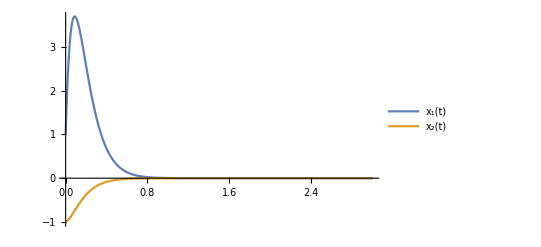

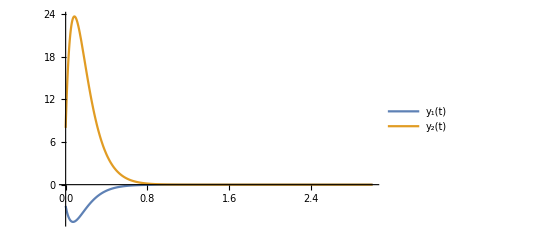

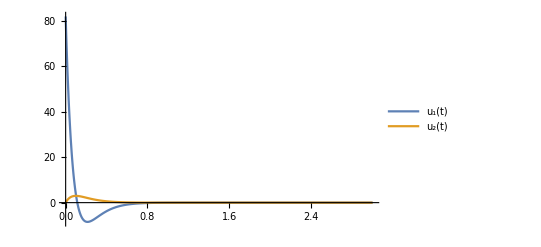

```mathematica
Plot[{Evaluate[x[t]/.CLSol]},{t,0,tmax}, PlotRange->All, PlotLegends->{ x[t]}]
Plot[{Evaluate[c . x[t]/.CLSol]},{t,0,tmax}, PlotRange->All, PlotLegends->{ "y_1(t)","y_2(t)"}]
Plot[{Evaluate[-K.x[t]/.CLSol]},{t,0,tmax}, PlotRange->All, PlotLegends->{ "u_1(t)", "u_2(t)"}]
```

# Question 3

```mathematica
Quit[]
```

## Part i) State Space Realization

### Construct N and D matrices.

```mathematica
N1[s]=({{1}, {s-1}, {s^2}});D1[s]={{s(s-1)(s+1)}};
Print["N(s) = ",N1[s],"\tD(s) = ",D1[s]]
N1[s].Inverse[D1[s]]==G[s]//ReleaseHold
```

N(s) = {{1},{-1+s},{s^2}}	D(s) = {{(-1+s) s (1+s)}}

{{1/((-1+s) s (1+s))},{1/(s (1+s))},{s/((-1+s) (1+s))}}==G[s]

```mathematica
Print["det(D(s)) = ",Det[D1[s]],"\nThe minimum number of states is ",Exponent[Det[D1[s]],s]]
```

det(D(s)) = (-1+s) s (1+s)
The minimum number of states is 3

### Find the GRCD:

Make: DN(s)=(D(s)
N(s))

```mathematica
DN[s]=Join[D1[s],N1[s]];TraditionalForm[DN[s]]
```

((s-1) s (s+1)
1
s-1
s^2)

#### ExtendedHermiteForm and other helpful functions given in course documents:

ExtendedHermiteForm[A,s] yields the Hermite form H of a matrix A of polynomials in s. The result is a list {H,U} such that H=U.A with U unimodular

```mathematica
myBlockDiagonalMatrix[b:{__?MatrixQ}]:=Module[{r,c,n=Length[b],i,j},{r,c}=Transpose[Dimensions/@b];
ArrayFlatten[Table[If[i==j,b[[i]],ConstantArray[0,{r[[i]],c[[j]]}]],{i,n},{j,n}]]];
FindMin[at_,kt_,xt_,pt_]:=Module[{a=at,k=kt,x=xt,p=pt,i,rgmin,degmin},For[i=k;rgmin=k;degmin=+Infinity,i≤p,i++,If[a[[i]]=!=0&&Exponent[a[[i]],x]<degmin,rgmin=i;
degmin=Exponent[a[[i]],x]]];
rgmin];

Variabile[at_]:=Module[{a=at,xt},xt=Variables[a];
If[xt==={},d,xt[[1]]]];

ExtPolQ[lt_List,xt_:{}]:=Module[{x=xt},
If[x==={}&&Length[Variables[lt]]>1,Message[General::badarg];
Return[$Failed],If[x==={},x=Variabile[lt]]];
(*If all the components of lt are polynomials in x*)Apply[And,PolynomialQ[#,x]&/@Flatten[lt]]||(*or in x^-1,the function returns True,False otherwise.(Substituting all the symbols x^-n->x^n we can use PolynomialQ also in this case)*)Apply[And,PolynomialQ[#,x]&/@Flatten[Expand[lt]/.{(x^(n:_))->(x^-n),x->x^-1}]]];

ExtendedHermiteForm[at_,xt_:{}]:=Module[{a=at,p,m,x=xt,u,v,k,kcl,i,j,q,deg,esp,coef,rg,rmin,upc,lpc,ch=False},If[x==={}&&Length[Variables[a]]>1,Message[General::badarg];
Return[$Failed],If[x==={},x=Variabile[a]]];
If[Not[ExtPolQ[a,x]],Message[General::pol];Return[$Failed]];
If[Not[Apply[And,PolynomialQ[#,x]&/@Flatten[a]]],a=a/.{(x^(n:_))->(x^-n)};
ch=True];
(*Initialize the variables*){p,m}=Dimensions[a];
u=IdentityMatrix[p];
(*Main loop on k (and kcl)*)For[k=1;kcl=1,k≤p&&kcl≤m,k++,(*Find the first non-zero element in row k*)While[a[[Range[k,p],kcl]]===Table[0,{p-k+1}]&&kcl<m,kcl++];
(*With this loop we eliminate all the elements in column kcl below position k*)While[If[k==p,False,a[[Range[k+1,p],kcl]]=!=Table[0,{p-k}]],(*Put the least degree element within column kcl in position (k,kcl)*)rmin=FindMin[Transpose[a][[kcl]],k,x,p];
If[rmin≠k,a=a/.{a[[rmin]]->a[[k]],a[[k]]->a[[rmin]]};
u=u/.{u[[rmin]]->u[[k]],u[[k]]->u[[rmin]]}];
(*Lower the degree of non-zero polynomials in column kcl below a[[k,kcl]]*)For[i=k+1,i≤p,i++,If[a[[i,kcl]]=!=0,lpc=PolynomialQuotient[a[[i,kcl]],a[[k,kcl]],x];
a=ReplacePart[a,Together[a[[i]]-a[[k]]*lpc],i];
u=ReplacePart[u,Expand[u[[i]]-u[[k]]*lpc],i]]]];(*Endwhile*)(*In column kcl lower the degree of polynomials above a[[k,kcl]] having the degree higher than that of a[[k,kcl]]*)If[a[[k,kcl]]=!=0,For[i=1,i<k,i++,If[a[[i,kcl]]=!=0,If[Exponent[a[[i,kcl]],x]≥Exponent[a[[k,kcl]],x],lpc=PolynomialQuotient[a[[i,kcl]],a[[k,kcl]],x];
a=ReplacePart[a,Together[a[[i]]-a[[k]]*lpc],i];
u=ReplacePart[u,Expand[u[[i]]-u[[k]]*lpc],i]]]]];
(*Make a[[k,kcl]] monic*)If[a[[k,kcl]]=!=0,lpc=Coefficient[a[[k,kcl]],x,Exponent[a[[k,kcl]],x]];
If[lpc=!=1,a=ReplacePart[a,Expand[a[[k]]/lpc],k];
u=ReplacePart[u,Expand[u[[k]]/lpc],k]]];
kcl++];(*Endfor*)(*Put all the zero rows in the last positions*)For[k=1,k<p,k++,If[a[[k]]===Table[0,{m}],i=p;
While[a[[i]]===Table[0,{m}]&&i>k,i=i-1];
If[i>k,For[j=k,j≤i,j++,a=ReplacePart[a,a[[j+1]],j];
u=ReplacePart[u,u[[j+1]],j]]];](*endif*)];(*endfor*)If[ch,{a,u}={a,u}/.{x^(n:_)->x^-n,x->x^-1}];
{a,u}]/;MatrixQ[at]||Message[General::mtrx,"ExtendedHermiteForm"];
```

SetDelayed::write: Tag BlockDiagonalMatrix in BlockDiagonalMatrix[b : {__?MatrixQ}] is Protected.

### Minimal Order State Space Realization

```mathematica
Clear[H,U]
{H[s],U[s]}=ExtendedHermiteForm[DN[s],s]; 
H[s]//TraditionalForm
 U[s]//Simplify//TraditionalForm;
Wg[s]=Take[H[s],Length[D1[s]]];
Print["W_g(s) = ",Wg[s]]
```

(1
0
0
0)

W_g(s) = {{1}}

W_g(s) = I. 
Realization already has the minimal number of states.

### Controller Form Realization of MFD

```mathematica
Print["D(s) = ",D1[s]//Expand]
```

D(s) = {{-s+s^3}}

```mathematica
j=Length[D1[s]];
k=Table[Max[Exponent[D1[s]ᵀ[[i]],s]],{i,1,j}];
S[s]=DiagonalMatrix[s^k];
Dhc=Coefficient[D1[s]ᵀ,s^k]ᵀ;
Print["k = ",k//MatrixForm,";\tS(s) = ",S[s],";\t D_hc = ",Dhc]
```

k = (3);	S(s) = {{s^3}};	 D_hc = {{1}}

#### Build up ψ(s), L(s), and D_lc :

```mathematica
L[s]=D1[s]-Dhc.S[s]//Expand;Print["L(s) = ",L[s]]
```

L(s) = {{-s}}

```mathematica
p2=Table[{Reverse[s^Range[0,k[[i]]-1]]},{i,1,j}]
ψ[s]=myBlockDiagonalMatrix[p2]ᵀ
```

{{{s^2,s,1}}}

{{s^2},{s},{1}}

```mathematica
d2=Array[Subscript[d, ##]&,{j,Total[k]}];
sol1=SolveAlways[Thread[Flatten[L[s]]==Flatten[d2.ψ[s]]],s]//Flatten;
Dlc=d2/.sol1;Print["D_lc = ",Dlc]
```

D_lc = {{0,-1,0}}

```mathematica
Dlc.ψ[s]+Dhc.S[s]
```

{{-s+s^3}}

#### Build up A_c^0 and B_c^0:

```mathematica
Ai=Table[DiagonalMatrix[ConstantArray[1,Max[k[[i]]-1,1]],-1,k[[i]]],{i,1,j}];
Ac0=myBlockDiagonalMatrix[Ai];
Bi=Table[{UnitVector[k[[i]],1]},{i,1,j}];Bc0=myBlockDiagonalMatrix[Bi]ᵀ;Print["A",Ac0,"\t B_c^0 = ",Bc0]
```

A{{0,0,0},{1,0,0},{0,1,0}}	 B_c^0 = {{1},{0},{0}}

#### Obtain the matrices for the controller - form state space realization :

```mathematica
A=Ac0-Bc0.Inverse[Dhc].Dlc;
B=Bc0.Inverse[Dhc];
```

```mathematica
nlc2=Array[Subscript[nlc, ##]&,{Length[N1[s]],Total[k]}];
sol2=SolveAlways[Thread[Flatten[N1[s]]==Flatten[nlc2.ψ[s]]],s]//Flatten;
Cm=nlc2/.sol2;
```

```mathematica
Print["A",A //TraditionalForm,"\t B_c = ",B //TraditionalForm,"\t C = ",Cm //TraditionalForm]
```

A(0 | 1 | 0
1 | 0 | 0
0 | 1 | 0)	 B_c = (1
0
0)	 C = (0 | 0 | 1
0 | 1 | -1
1 | 0 | 0)

State Space Realization is found!

### State Space Eqns

```mathematica
x[t_]:=Array[Subscript[x, #][t]&,Total[k]]
y[t_]:=Array[Subscript[y, #][t]&,Length[N1[s]]]
u[t_]:=Array[Subscript[u, #][t]&,Length[Bcᵀ]]
```

```mathematica
SSEQ=Thread[D[x[t],t]==A.x[t]+B.u[t]]//Chop;ColumnForm[SSEQ]
OEQ=Thread[y[t]==Cm.x[t]]//Chop;ColumnForm[OEQ]
```

x_1'[t]==u_1[t]+x_2[t]
x_2'[t]==x_1[t]
x_3'[t]==x_2[t]

y_1[t]==x_3[t]
y_2[t]==x_2[t]-x_3[t]
y_3[t]==x_1[t]

## Part ii)

### Find Q, Sf and R matrices Sf=0; Q=100 I and R= 0.01 I

```mathematica
Iy=IdentityMatrix[Length[y[t]]]
Iu=IdentityMatrix[Length[u[t]]]
n=Length[A];
```

{{1,0,0},{0,1,0},{0,0,1}}

{{1}}

```mathematica
Sf=ConstantArray[0,Dimensions[Iy]];Q=100 Iy;R=0.01Iu;tf=10;
Print["S",Sf //MatrixForm,"\t Q = ",Q //MatrixForm,"\t R = ",R //MatrixForm]
```

S(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)	 Q = (100 | 0 | 0
0 | 100 | 0
0 | 0 | 100)	 R = (0.01)

### Riccati Equation (tf is finite)

```mathematica
S[t_]:=Array[Subscript[S,Sequence@@Through[{Min,Max}[##]]][t]&,{n,n}]
S[t]
LHRE=D[S[t],t]+S[t].A-S[t].B.Inverse[R].Bᵀ.S[t]+Cmᵀ.Q.Cm+Aᵀ.S[t]
```

{{S_(1,1)[t],S_(1,2)[t],S_(1,3)[t]},{S_(1,2)[t],S_(2,2)[t],S_(2,3)[t]},{S_(1,3)[t],S_(2,3)[t],S_(3,3)[t]}}

{{100.-100. (S_(1,1)[t])^2+2 S_(1,2)[t]+S_(1,1)'[t],0.+S_(1,1)[t]-100. S_(1,1)[t] S_(1,2)[t]+S_(1,3)[t]+S_(2,2)[t]+S_(1,2)'[t],0.-100. S_(1,1)[t] S_(1,3)[t]+S_(2,3)[t]+S_(1,3)'[t]},{0.+S_(1,1)[t]-100. S_(1,1)[t] S_(1,2)[t]+S_(1,3)[t]+S_(2,2)[t]+S_(1,2)'[t],100.+2 S_(1,2)[t]-100. (S_(1,2)[t])^2+2 S_(2,3)[t]+S_(2,2)'[t],-100.+S_(1,3)[t]-100. S_(1,2)[t] S_(1,3)[t]+S_(3,3)[t]+S_(2,3)'[t]},{0.-100. S_(1,1)[t] S_(1,3)[t]+S_(2,3)[t]+S_(1,3)'[t],-100.+S_(1,3)[t]-100. S_(1,2)[t] S_(1,3)[t]+S_(3,3)[t]+S_(2,3)'[t],200.-100. (S_(1,3)[t])^2+S_(3,3)'[t]}}

Due to symmetry there are duplicate equations :

```mathematica
Clear[i,j]
```

#### Eliminate duplicate equations:

```mathematica
UpperElements[M_]:=Flatten[Table[M[[i,j]],{i,Length[M]},{j,i,Length[M]}]]
LHREup=UpperElements[LHRE];
Ov=ConstantArray[0,Length[LHREup]];
RE=Thread[LHREup==Ov];
Sv[t_]:=UpperElements[S[t]]
Print["RE: ",RE//MatrixForm]
```

RE: (100.-100. (S_(1,1)[t])^2+2 S_(1,2)[t]+S_(1,1)'[t]==0
0.+S_(1,1)[t]-100. S_(1,1)[t] S_(1,2)[t]+S_(1,3)[t]+S_(2,2)[t]+S_(1,2)'[t]==0
0.-100. S_(1,1)[t] S_(1,3)[t]+S_(2,3)[t]+S_(1,3)'[t]==0
100.+2 S_(1,2)[t]-100. (S_(1,2)[t])^2+2 S_(2,3)[t]+S_(2,2)'[t]==0
-100.+S_(1,3)[t]-100. S_(1,2)[t] S_(1,3)[t]+S_(3,3)[t]+S_(2,3)'[t]==0
200.-100. (S_(1,3)[t])^2+S_(3,3)'[t]==0)

#### Solve RE :

```mathematica
solS=NDSolve[{RE,Thread[Sv[tf]==UpperElements[Cmᵀ.Sf.Cm]]},Sv[t],{t,0,tf}]//Quiet//Flatten;
(*Table[Plot[Evaluate[Sv[t][[i]]/.SolS],{t,0,tf}, PlotRange->{{0,tf},All},PlotLabel->Subscript["Sv", i]],{i,1,Length[Sv[t]]}]*)
```

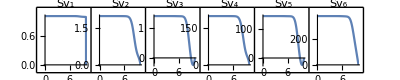

```mathematica
(*For[i=1,i<=Length[Sv[t]],i++,Print[Plot[Evaluate[Sv[t][[i]]/.solS],{t,0,tf}, PlotRange->{{0,tf},All},PlotLabel->Subscript["Sv", i]]]]*)
GraphicsGrid[{Table[Plot[Evaluate[Sv[t][[i]]/.solS],{t,0,tf}, PlotRange->{{0,tf},All},AspectRatio->Full,PlotLabel->ToString[Subscript["Sv", i], StandardForm]],{i,1,Length[Sv[t]]}]},Frame->All]
```

#### LQR gain matrix :

{{100. S_(1,1)[t],100. S_(1,2)[t],100. S_(1,3)[t]}}

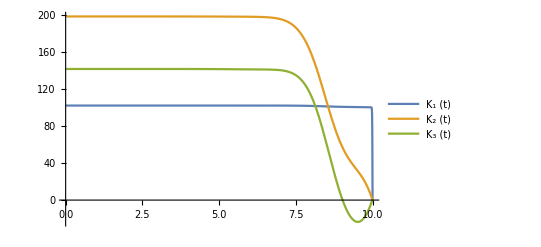

```mathematica
Clear[Kop]
Kop[t_]:=(Inverse[R].Bᵀ .S[t])
Kop[t]//Chop
Plot[Evaluate[Kop[t]/.solS],{t,0,tf}, PlotRange->All,PlotLegends->Array[Subscript["K", #]"(t)"&,3]]
```

### State Equation :

```mathematica
uop[t_]:=-Kop[t].x[t]
StEqn=Thread[D[x[t],t]==A.x[t]+B.uop[t]]//Chop;
ColumnForm[StEqn]
```

x_1'[t]==x_2[t]-100. x_1[t] S_(1,1)[t]-100. x_2[t] S_(1,2)[t]-100. x_3[t] S_(1,3)[t]
x_2'[t]==x_1[t]
x_3'[t]==x_2[t]

### Tracking eqns:

```mathematica
ξ[t_]:=Array[Subscript[ξ, #][t]&,n];
w[t_]:=Array[Subscript[w, #][t]&,n];
η[t_]:=Array[Subscript[η, #][t]&,n];
ξEq=Thread[-D[ξ[t],t]+S[t].B.Inverse[R].Bᵀ.ξ[t]+S[t].w[t]-Cmᵀ.Q.η[t]-Aᵀ.ξ[t]==Table[0,Length[ξ[t]]]]/.Thread[w[t]->{0,0,0}]//Chop; (*S[t] yerine Sr koyarsan olur zamanla degismeyen K icin.*)
ColumnForm[ξEq]
```

-100 η_3[t]-ξ_2[t]+100. ξ_1[t] S_(1,1)[t]-ξ_1'[t]==0
-100 η_2[t]-ξ_1[t]-ξ_3[t]+100. ξ_1[t] S_(1,2)[t]-ξ_2'[t]==0
-100 η_1[t]+100 η_2[t]+100. ξ_1[t] S_(1,3)[t]-ξ_3'[t]==0

#### Desired tracking

```mathematica
yd[t_]:=ao Cos[ω t]
η[t_]:={yd[t],yd'[t],yd''[t]};Print["η(t) = ",η[t]//MatrixForm]
ξEq=Thread[-D[ξ[t],t]+S[t].B.Inverse[R].Bᵀ.ξ[t]+S[t].w[t]-Cmᵀ.Q.η[t]-Aᵀ.ξ[t]==Table[0,Length[ξ[t]]]]/.Thread[w[t]->{0,0,0}]//Chop;
ColumnForm[ξEq]
```

η(t) = (ao Cos[t ω]
-ao ω Sin[t ω]
-ao ω^2 Cos[t ω])

100 ao ω^2 Cos[t ω]-ξ_2[t]+100. ξ_1[t] S_(1,1)[t]-ξ_1'[t]==0
100 ao ω Sin[t ω]-ξ_1[t]-ξ_3[t]+100. ξ_1[t] S_(1,2)[t]-ξ_2'[t]==0
-100 ao Cos[t ω]-100 ao ω Sin[t ω]+100. ξ_1[t] S_(1,3)[t]-ξ_3'[t]==0

## Part iii) Simulation

Given values:

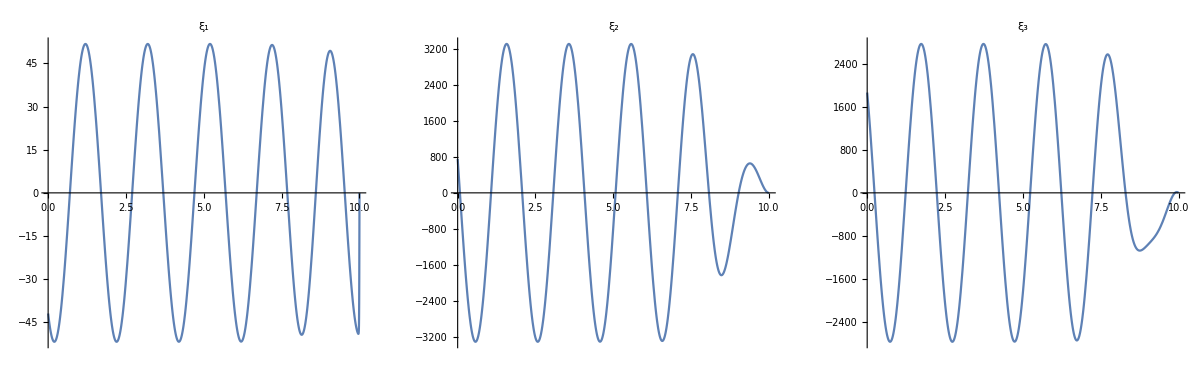

```mathematica
Vals={ao->5,ω->π};
Solξ=NDSolve[{ξEq/.solS,Thread[ξ[tf]==Cmᵀ.Sf.η[tf]]}/.Vals//Flatten,ξ[t],{t,0,tf}]//Flatten;
GraphicsGrid[{Table[Plot[Evaluate[ξ[t][[i]]/.Solξ],{t,0,tf}, PlotRange->All,PlotLabel->Subscript[ξ, i], AspectRatio->1],{i,1,Length[ξ[t]]}]}]
```

### State Responses

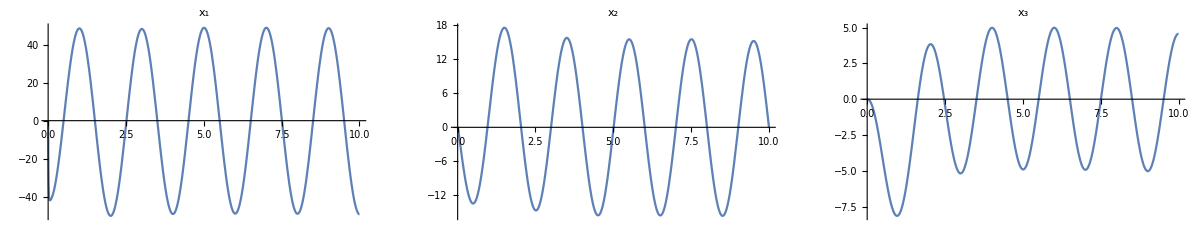

```mathematica
u[t_]:=-Kop[t].x[t]+Inverse[R].Bᵀ.ξ[t]
Solx=NDSolve[{(D[x[t],t]==A .x[t]+B.u[t]/.Vals/.solS/.Solξ),x[0]=={0,0,0}},x[t],{t,0,tf}][[1]];
GraphicsGrid[{Table[Plot[Evaluate[x[t][[i]]/.Solx],{t,0,tf}, PlotRange->All,PlotLabel->Subscript["x", i]],{i,1,Length[x[t]]}]}]
```

### Output Plot :

```mathematica
yo[t_]:=(Cm.x[t])/.Solx
```

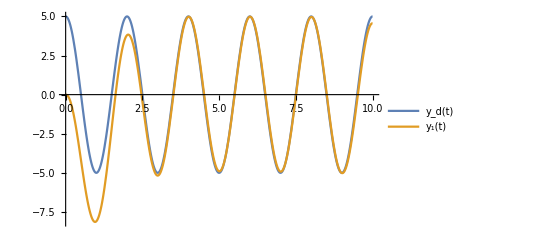

```mathematica
Plot[{yd[t]/.Vals,yo[t][[1]]},{t,0,tf}, PlotLegends->{"y_d(t)",y[t][[1]]}]
```

First Derivative

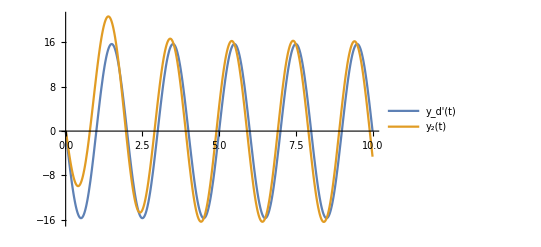

```mathematica
Plot[{yd'[t]/.Vals//Chop,yo[t][[2]]},{t,0,tf}, PlotLegends->{"y_d'(t)",y[t][[2]]}]
```

Second Derivative

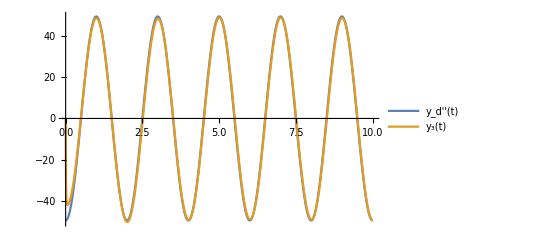

```mathematica
Plot[{yd''[t]/.Vals//Chop,yo[t][[3]]},{t,0,tf}, PlotLegends->{"y_d''(t)",y[t][[3]]}]
```

### Tracking Error Plot:

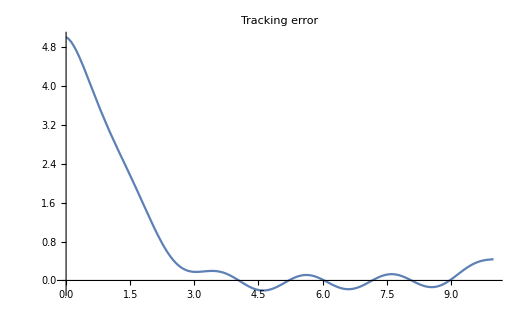

```mathematica
Plot[{yd[t]-yo[t][[1]]/.Solx/.Vals},{t,0,tf}, PlotLabel->"Tracking error", PlotRange->All]
```

Velocity Error :

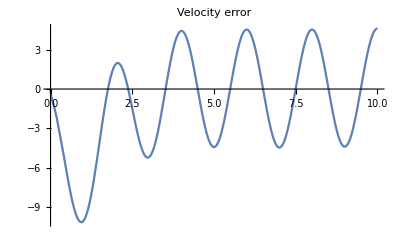

```mathematica
Plot[{yd'[t]-yo[t][[2]]/.Solx/.Vals},{t,0,tf}, PlotLabel->"Velocity error", PlotRange->All]
```

Acceleration Error :

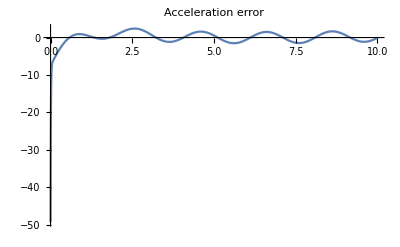

```mathematica
Plot[{yd''[t]-yo[t][[3]]/.Solx/.Vals},{t,0,tf}, PlotLabel->"Acceleration error", PlotRange->All]
```

## Objective Function value calculation :

Define tracking error as z :

```mathematica
z[t_]:=η[t]-yo[t]
J=1/2 NIntegrate[(z[t].Q.z[t]+u[t].R.u[t])/.Vals/.solS/.Solx/.Solξ,{t,0,tf},AccuracyGoal->6]
```

12146.5

#### System operates as desired. Tracking can be done successfully!